```mathematica
fanGen={{0,0},{1,0},{0,-1},{-1,0},{0,1}};
```

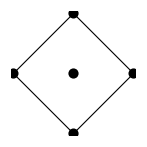

```mathematica
Graphics[{EdgeForm[Black],FaceForm[],Polygon@Take[fanGen,-4], PointSize[.05],Point@fanGen}]
```

```mathematica
fanV = ArrayPad[fanGen, {{0,0}, {0,1}}, 1]
```

{{0,0,1},{1,0,1},{0,-1,1},{-1,0,1},{0,1,1}}

```mathematica
Solve[Thread[fanVᵀ.Array[a,5]==0], Array[a,5], Integers]
fanQ = Array[a,5]/.First[%]/.{{C[1]->-1,C[2]->1},{C[1]->-1,C[2]->0}}
fanVQ = Join[fanVᵀ, %]ᵀ;
fanVQ//MatrixForm
```

{{a[1]→ConditionalExpression[2 C[1], (C[1]|C[2])∈ℤ],a[2]→ConditionalExpression[C[2], (C[1]|C[2])∈ℤ],a[3]→ConditionalExpression[-C[1]-C[2], (C[1]|C[2])∈ℤ],a[4]→ConditionalExpression[C[2], (C[1]|C[2])∈ℤ],a[5]→ConditionalExpression[-C[1]-C[2], (C[1]|C[2])∈ℤ]}}

{{-2,1,0,1,0},{-2,0,1,0,1}}

(0 | 0 | 1 | -2 | -2
1 | 0 | 1 | 1 | 0
0 | -1 | 1 | 0 | 1
-1 | 0 | 1 | 1 | 0
0 | 1 | 1 | 0 | 1)

```mathematica
CSMDef = Thread[Array[z,Length[fanQ]]->Table[Product[a[i]^fanQ[[A, i]], {i,1,5}], {A, 1, Length[fanQ]}]]
```

{z[1]→(a[2] a[4])/a[1]^2,z[2]→(a[3] a[5])/a[1]^2}

```mathematica
H[X_,Y_]=Sum[a[i]X^fanVQ[[i,1]]Y^fanVQ[[i,2]], {i,Length[fanVQ]}]
```

a[1]+X a[2]+a[3]/Y+a[4]/X+Y a[5]

```mathematica
H[X,Y]/a[1]/.{X->xc X, Y->yc Y}//Expand
H1[X_,Y_]=%/.{xc->a[1]/a[2], yc->a[1]/a[5]}/.{(a[2] a[4])/a[1]^2->z[1],(a[3] a[5])/a[1]^2->z[2]}
```

1+(X xc a[2])/a[1]+a[3]/(Y yc a[1])+a[4]/(X xc a[1])+(Y yc a[5])/a[1]

1+X+Y+z[1]/X+z[2]/Y

## Periods from gamma soln

```mathematica
Gamma/@(fanQᵀ.{n1+r1,n2+r2}+1)
z1^n1 z2^n2/Times@@%
%/.{Gamma[1-2 (n1+r1)-2 (n2+r2)]->2Pi (n1+n2+r1+r2)/Sin[2Pi (n1+n2+r1+r2)]/Gamma[1+2 (n1+n2+r1+r2)]}
FullSimplify[D[%, r1, r2]/.{r1->0,r2->0}, (n1|n2)∈PositiveIntegers]
```

{Gamma[1-2 (n1+r1)-2 (n2+r2)],Gamma[1+n1+r1],Gamma[1+n2+r2],Gamma[1+n1+r1],Gamma[1+n2+r2]}

(z1^n1 z2^n2)/(Gamma[1+n1+r1]^2 Gamma[1+n2+r2]^2 Gamma[1-2 (n1+r1)-2 (n2+r2)])

(z1^n1 z2^n2 Gamma[1+2 (n1+n2+r1+r2)] Sin[2 π (n1+n2+r1+r2)])/(2 π (n1+n2+r1+r2) Gamma[1+n1+r1]^2 Gamma[1+n2+r2]^2)

-1/((n1+n2)^2 (n1!)^2 (n2!)^2)2 z1^n1 z2^n2 (2 (n1+n2))! (1+(n1+n2) (HarmonicNumber[n1]+HarmonicNumber[n2]-2 HarmonicNumber[2 (n1+n2)]))

## Check

```mathematica
Table[Sum[(2n-1)!/Factorial[n-l]^2/Factorial[l]^2 lam^l, {l,0,n}]z^n, {n, 1, 10}]//Simplify
```

{(1+lam) z,3/2 (1+4 lam+lam^2) z^2,10/3 (1+9 lam+9 lam^2+lam^3) z^3,35/4 (1+16 lam+36 lam^2+16 lam^3+lam^4) z^4,126/5 (1+25 lam+100 lam^2+100 lam^3+25 lam^4+lam^5) z^5,77 (1+36 lam+225 lam^2+400 lam^3+225 lam^4+36 lam^5+lam^6) z^6,1716/7 (1+49 lam+441 lam^2+1225 lam^3+1225 lam^4+441 lam^5+49 lam^6+lam^7) z^7,6435/8 (1+64 lam+784 lam^2+3136 lam^3+4900 lam^4+3136 lam^5+784 lam^6+64 lam^7+lam^8) z^8,24310/9 (1+81 lam+1296 lam^2+7056 lam^3+15876 lam^4+15876 lam^5+7056 lam^6+1296 lam^7+81 lam^8+lam^9) z^9,46189/5 (1+100 lam+2025 lam^2+14400 lam^3+44100 lam^4+63504 lam^5+44100 lam^6+14400 lam^7+2025 lam^8+100 lam^9+lam^10) z^10}

## Check the version in notes

```mathematica
(* varpi2 with Richardson *)
varpi2[z_,lam_]:=With[{Nn=200, d=5}, Module[{terms,sums}, 
terms=Table[Sum[(2n-1)!/Factorial[n-l]^2/Factorial[l]^2 lam^l, {l,0,n}]z^n, {n, 1, Nn}];
sums=Log[z]+2Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
(* varpi3 with Richardson *)
varpi3[z_,lam_]:=With[{Nn=200, d=5}, Module[{terms,sums}, 
terms=Table[Sum[(2n)!/n/Factorial[n-l]^2/Factorial[l]^2(HarmonicNumber[n-l]+HarmonicNumber[l]-2HarmonicNumber[2n]+1/n) lam^l, {l,0,n}]z^n, {n, 1, Nn}];
sums=-Log[z]^2+(2Log[z]+Log[lam])Last[varpi2[z,lam]]-2Accumulate[terms];
Table[Sum[sums[[n+k]](n+k)^d(-1)^(k+d)/k!/(d-k)!, {k, 0, d}], {n, 1, Length[sums]-d}]
]];
```

```mathematica
With[{lam=N[1, 300]}, Last@varpi2[1/4/(1+Sqrt[lam])^2, lam]]
```

-2.332487232246550104833404764376905005537308887089831170881329150497302342366406971206343421840927296712112374573772157707978009457834341793671067838130294836241584304091290138276630742843918959710674903290165479284347374816300358840732247701560210036211639664775889229975436642365146251362

```mathematica
-8Catalan/Pi//N[#, 100]&
```

-2.332487232246550241107075651747159350912529231886698162088012552893981095043510893813014594425072471

```mathematica
With[{lam=N[1, 300]}, Last@varpi3[1/4/(1+Sqrt[lam])^2, lam]]
```

6.579736267392907161716559377663774613325048259486037097440017967898025112951056663676031108973582122928029375608479503726737171019638378737587680234925502150651684270675374751090819557436398913507361029123838453687230733166149955589078963192149082517129091319263398081069423693

```mathematica
2Pi^2/3//N
```

6.57974

```mathematica
Hypergeometric2F1
```